## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,6,7}]];
a0a1REFERENCE=a0a1NUCLmartinrimas[[All,{8,9}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 (r^2+rp^2)] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
SolveSecularF[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,c01_?NumberQ,a01_?NumberQ,c02_?NumberQ,a02_?NumberQ,TwoMyOverHBsq_?NumberQ]:=Block[{a00,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

a00={{c01,a01},{c02,a02}};

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nGrid=200;

nf={6,4}; (* number form for printing, only *)
k0FM=0.1;  (*initial momentum*)

rr=25.0;   (*Integration radius*)
αL=Get[LocalObject["3-1_CorePara_SwaveRimas"]]; (*what was the old αL for rimas*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.276473 MeV

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]
```

S- and P-wave phase shifts

```mathematica
nk=2;

(*Load Martin wave function*)

Martinϕ=Import["..\abc_u_4.0_binf_r1b.dnst"];
Mϕ=Transpose[{Martinϕ⟦All,1⟧,Sqrt[Martinϕ⟦All,3⟧]}];
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}]
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]]
Result=FindFit[Mϕ,wf,Flatten[core],r];
core=core/.Result;
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
Show[ListPlot[Mϕ,PlotRange->All],Plot[wf,{r,-1,Mϕ⟦-1,1⟧}],ImageSize->500]
core⟦All,1⟧=core⟦All,1⟧/core⟦1,1⟧;
core
```

Import::nffil: File ..\abc_u_4.0_binf_r1b.dnst not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],√Symbol[]} cannot be transposed.

C1 ⅇ^(-r^2 Α1)+C2 ⅇ^(-r^2 Α2)

FindFit::fitd: First argument Transpose[{Symbol[],√Symbol[]}] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[Transpose[{Symbol[],√Symbol[]}],C1 ⅇ^(-r^2 Α1)+C2 ⅇ^(-r^2 Α2),{C1,Α1,C2,Α2},r]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ListPlot::lpn: Transpose[{Symbol[],√Symbol[]}] is not a list of numbers or pairs of numbers.

Plot::plln: Limiting value Symbol[] in {r,-1,Symbol[]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Transpose[{Symbol[],√Symbol[]}],PlotRange→All],Plot[wf,{r,-1,Mϕ⟦-1,1⟧}],ImageSize→500].

Show[ListPlot[Transpose[{Symbol[],√Symbol[]}],PlotRange→All],Plot[wf,{r,-1,Mϕ⟦-1,1⟧}],ImageSize→500]

ReplaceAll::reps: {FindFit[Transpose[{Symbol[],√Symbol[]}],C1 ⅇ^(-r^2 Α1)+C2 ⅇ^(-r^2 Α2),{C1,Α1,C2,Α2},r]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Transpose[{Symbol[],√Symbol[]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitd: First argument ({C1,Α1}/.Transpose[{Symbol[],√Symbol[]}])/Α1 in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[({C1,Α1}/.Transpose[{Symbol[],√Symbol[]}])/Α1,C1 ⅇ^(-r^2 Α1)+C2 ⅇ^(-r^2 Α2),{C1,Α1,C2,Α2},r]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{({C1,Α1}/.Transpose[{Symbol[],√Symbol[]}])/C1,{C2,Α2}}/.FindFit[({C1,Α1}/.Transpose[{Symbol[],√Symbol[]}])/Α1,C1 ⅇ^(-r^2 Α1)+C2 ⅇ^(-r^2 Α2),{C1,Α1,C2,Α2},r]

```mathematica
GetERE[x_,y_,z_]:=Module[{Aa0=x,Cc1=y,Aa1=z},
core={{1.,Aa0},{Cc1,Aa1}};
f1=1;f2=4;
Print[core];
(*Do one iteraction for one WaveFunction*)
tanDsL={};tanDpL={};
tanDs={};tanDp={};
SetSharedVariable[tanDs,tanDp];
(*Parallelize over the momenta inspected*)
ParallelDo[
momFM=Sqrt[2 μ energ]/hbar;
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
exportTab={};
dataTab={};
Lrel = 0;
dataS=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)/tanDs⟦All,2⟧}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)^3/tanDp⟦All,2⟧}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;

(*exportTab has λ C1 α1 C2 α2 A0 r0 a1 r1*)
AppendTo[dataTab,{λ,core,a0tf,r0tf,a1tf,r1tf}];

(*Print me*)
λ=0.25 activeLEC⟦nn⟧[[1]]^2;
Print["λ = ",λ," Wf parameters",core,":  a_s = ",a0tf," fm    r_s = ",r0tf," fm        a_p = ",a1tf," fm^3     r_p = ",r1tf," fm"];
{λ,core,a0tf,r0tf,a1tf,r1tf}]
```

```mathematica
λ=0.25 activeLEC⟦nn⟧[[1]]^2;
GetERElean[x_?(VectorQ[#, NumericQ]&)]:=Module[{Aa0=x[[1]],Cc1=x[[2]],Aa1=x[[3]]},
core={{1.,Aa0},{Cc1,Aa1}};
f1=1;f2=4;
(*Do one iteraction for one WaveFunction*)
tanDsL={};tanDpL={};
tanDs={};tanDp={};
SetSharedVariable[tanDs,tanDp];
(*Parallelize over the momenta inspected*)
ParallelDo[
momFM=Sqrt[2 μ energ]/hbar;
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)/tanDs⟦All,2⟧}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;

Lrel = 1;
dataP=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)^3/tanDp⟦All,2⟧}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;

{a0tf,r0tf,a1tf}]
```

```mathematica
(*Configure calculations*)
ErangeMeV=N[findLogDivisions[{(k0FM hbar)^2/(2 μ)0.01,0.1},5]];
rr=10;nGrid=100;
k0FM=0.01;
nn=9;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;

Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]," ; c_1 = ",NumberForm[c1,nf]," ; α_1 = ",NumberForm[α1,nf]];
```

λ = Λ^2/4 = 16.0000  ⇒ Λ = 8.0000 ; C_0 = -1898.5500 ; D_0 = 25697 ; c_1 = c1 ; α_1 = α1

```mathematica
GetERElean[x_?(VectorQ[#, NumericQ]&)]:=x
```

```mathematica
GetERElean[{1,2,2}]
```

Power::infy: Infinite expression 1/0 encountered.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

{0.898743,-1.29517,-1/Fit[{{0.000601414,ComplexInfinity},{0.00190184,-9.2844},{0.00601414,-9.2848},{0.0190184,-9.2888}},{1,p^2},p]}

```mathematica
aini={123,534};
FindRoot[GetERElean[a],{a,aini}]
```

{a→{0.,0.}}

```mathematica
Terminal={};
Do[Do[Do[
Terminal=AppendTo[Terminal,GetERE[xa,xb,xc]];
,{xc,0.2,1,0.2}],{xb,0.2,1,0.2}],{xa,0.2,1,0.2}]
Terminal
```

{}

------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------
------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

Plotting       ϕ(r) = 0.361502 ⅇ^(-1.03041 r^2)+0.121219 ⅇ^(-0.178632 r^2)

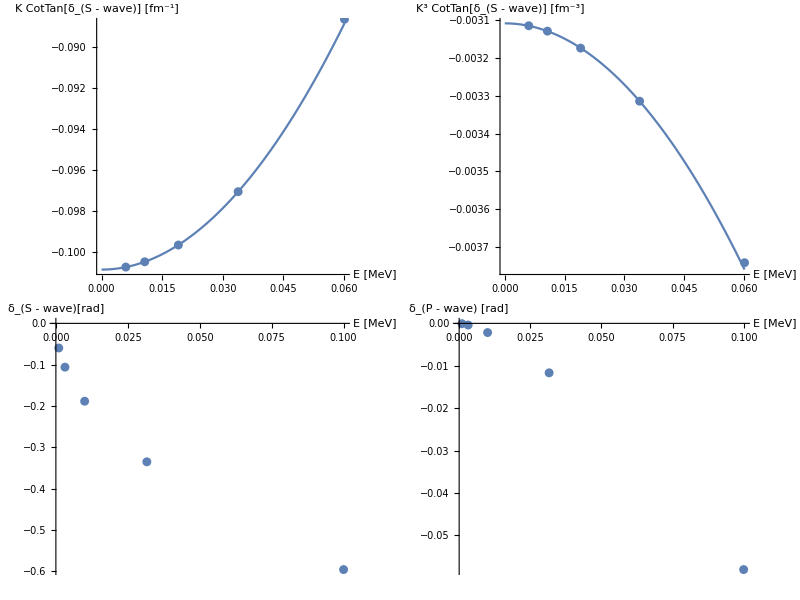

```mathematica
(*Plot the Phaseshifts for each α and C that I used*)
Print["Plotting       ϕ(r) = " ,wf];
phaseS=Table[Transpose[{tanDs⟦i,1⟧, ArcTan[tanDs⟦i,2⟧]}],{i,1,Length[tanDs⟦All,1⟧]}];
phaseP=Table[Transpose[{tanDp⟦i,1⟧, ArcTan[tanDp⟦i,2⟧]}],{i,1,Length[tanDp⟦All,1⟧]}];

Grid[{{

Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"}]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"}]

},
{Show[{
ListPlot[phaseS]},ImageSize->500,AxesLabel->{"E [MeV]","δ_(S - wave)[rad]"}],
Show[
ListPlot[phaseP,AxesLabel->{"E [MeV]","δ_(P - wave) [rad]"},ImageSize->500,PlotRange->{Automatic,Automatic},Joined->False]]}
}]
```

Part::take: Cannot take positions 1 through 10 in {{0.00601414,-0.100752},{0.0106948,-0.100493},{0.0190184,-0.0996731},{0.03382,-0.0970628},{0.0601414,-0.0886255}}.

Fit::fitd: First argument {{0.00601414,-0.100752},{0.0106948,-0.100493},{0.0190184,-0.0996731},{0.03382,-0.0970628},{0.0601414,-0.0886255}}⟦1;;10⟧ in Fit is not a list or a rectangular array.

Fit::fitd: First argument System`TSolveDump`P$6249[1] in Fit is not a list or a rectangular array.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {NSolve[-ⅈ p+Fit[{{«2»},{«2»},{«2»},{«2»},{«2»}}⟦1;;10⟧,{1,p^2,p^4,p^6},p]==0,{p}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

p/.NSolve[-ⅈ p+Fit[{{0.00601414,-0.100752},{0.0106948,-0.100493},{0.0190184,-0.0996731},{0.03382,-0.0970628},{0.0601414,-0.0886255}}⟦1;;10⟧,{1,p^2,p^4,p^6},p]==0,{p}]

27.6473 (p/.NSolve[-ⅈ p+Fit[{{0.00601414,-0.100752},{0.0106948,-0.100493},{0.0190184,-0.0996731},{0.03382,-0.0970628},{0.0601414,-0.0886255}}⟦1;;10⟧,{1,p^2,p^4,p^6},p]==0,{p}])^2

General::ivar: 8.17143×10^-6 is not a valid variable.

General::ivar: 0.00817144 is not a valid variable.

General::ivar: 0.0163347 is not a valid variable.

General::ivar: 0.024498 is not a valid variable.

General::ivar: 0.0326612 is not a valid variable.

General::ivar: 0.0408245 is not a valid variable.

General::ivar: 0.0489878 is not a valid variable.

General::ivar: 0.057151 is not a valid variable.

General::ivar: 0.0653143 is not a valid variable.

General::ivar: 0.0734776 is not a valid variable.

General::ivar: 0.0816408 is not a valid variable.

General::ivar: 0.0898041 is not a valid variable.

General::ivar: 0.0979674 is not a valid variable.

General::ivar: 0.106131 is not a valid variable.

General::ivar: 0.114294 is not a valid variable.

General::ivar: 0.122457 is not a valid variable.

General::ivar: 0.13062 is not a valid variable.

General::ivar: 0.138784 is not a valid variable.

General::ivar: 0.146947 is not a valid variable.

General::ivar: 0.15511 is not a valid variable.

General::ivar: 0.163273 is not a valid variable.

General::ivar: 0.171437 is not a valid variable.

General::ivar: 0.1796 is not a valid variable.

General::ivar: 0.187763 is not a valid variable.

General::ivar: 0.195927 is not a valid variable.

General::ivar: 0.20409 is not a valid variable.

General::ivar: 0.212253 is not a valid variable.

General::ivar: 0.220416 is not a valid variable.

General::ivar: 0.22858 is not a valid variable.

General::ivar: 0.236743 is not a valid variable.

General::ivar: 0.244906 is not a valid variable.

General::ivar: 0.253069 is not a valid variable.

General::ivar: 0.261233 is not a valid variable.

General::ivar: 0.269396 is not a valid variable.

General::ivar: 0.277559 is not a valid variable.

General::ivar: 0.285722 is not a valid variable.

General::ivar: 0.293886 is not a valid variable.

General::ivar: 0.302049 is not a valid variable.

General::ivar: 0.310212 is not a valid variable.

General::ivar: 0.318376 is not a valid variable.

General::ivar: 0.326539 is not a valid variable.

General::ivar: 0.334702 is not a valid variable.

General::ivar: 0.342865 is not a valid variable.

General::ivar: 0.351029 is not a valid variable.

General::ivar: 0.359192 is not a valid variable.

General::ivar: 0.367355 is not a valid variable.

General::ivar: 0.375518 is not a valid variable.

General::ivar: 0.383682 is not a valid variable.

General::ivar: 0.391845 is not a valid variable.

General::ivar: 0.4 is not a valid variable.

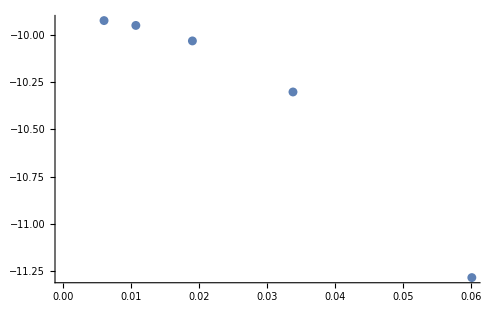

```mathematica
Tfit=(Fit[dataS⟦1;;10⟧,{1,p^2,p^4,p^6},p]);
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
(*Show[ListPlot[dataS],Plot[Tfit,{p,-1,0.5}],ImageSize->500]*)
Polesp=(p/.NSolve[Tfit-ⅈ p==0,{p}]) 
PolesE=hbar^2 Polesp^2 / (2 μ)
Show[ListPlot[dataTS],Plot[Tfit^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500]
```